```mathematica
(* Potential, without normalization *)
V[θ_] = 1-θ^4; (*θ is now ϕ/μ*)

(* Putting in required known constants *)
m = 1.2209*10^19 ; (*Non-reduced Planck Mass, Subscript[m, pl], in GeV/c^2 *)
Mmin = 0.5; (*M is Subscript[m, pl]/μ *)
Mmax = 2;
δ = 4.5*10^-5 ;(*I think this is the current value I'm using*)

(* Slow-roll parameters *)
ϵ[θ_,M_] := M^2/(16 π)(V'[θ]/V[θ])^2
(* Field Value at the end of inflation *)
θe[M_] := Re[X/. FindRoot[ϵ[X,M]==1,{X,M/√π}]]
Nume[θ_?NumberQ,M_]:=Re[(8 π/M^2) NIntegrate[V[b]/V'[b],{b, θe[M],θ}]]

(* Field value NN e-folds before the end of inflation. Exact answer: *)
θN[NN_,M_] := Re[xx/. FindRoot[Nume[xx,M] == NN, {xx,θe[M]}]]

(* Normalization *)
Vend[NN_,M_]:= (3 δ^2 M^2)/(128π)(V'[θN[NN,M]]/V[θN[NN,M]])^2(V[θe[M]]/V[θN[NN,M]])

(* Reheat Temperature *)
Trh[NN_,M_]:=Vend[NN,M]^(1/4)

(* Max N *)
NM[M_] := Re[xy/. FindRoot[xy-Log[Trh[xy,M]]==68,{xy,60}]]
```

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[ϵ[X,MM]==1,{X,MM/(√π)}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

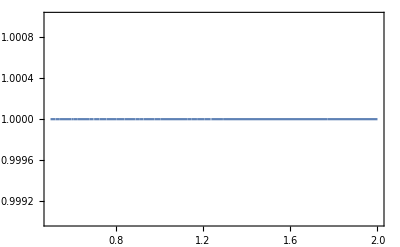

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {-0.936278}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {-0.936278}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {-0.936278}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,0.500031]==xy,{xx,θe[0.500031]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {0.00580109}. NIntegrate obtained 5.89492×10^10 and 5.89492×10^10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM/(√π)} is not a number or array of numbers.

FindRoot::srect: Value 0.56419 MM in search specification {X,MM 0.56419} is not a number or array of numbers.

General::stop: Further output of FindRoot::srect will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

Plot::exclul: {0.003943 ((MM^2 (1-Power[«2»]) Re[ReplaceAll[«2»]]^6)/(1+Times[«2»])^3)^(1/4)-0,Re[xy/.FindRoot[xy+Times[«2»]==68,{xy,60}]]-0,0.003943 Im[((MM^2 (1+Times[«2»]) Re[«1»]^6)/Plus[«2»]^3)^(1/4)]-0} must be a list of equalities or real-valued functions.

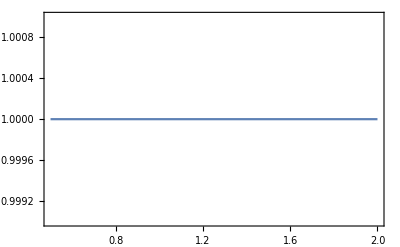

```mathematica
(*Consistency Checks*)
Plot[ϵ[θe[MM],MM],{MM,Mmin,Mmax},Axes->False,Frame->True,PlotRange->{0.999,1.001}]
Plot[Nume[θN[NM[MM],MM],MM]/NM[MM],{MM,Mmin,Mmax},Axes->False,Frame->True,PlotRange->{0.999,1.001}]
```

```mathematica
Nlist=Array[NM[#*0.1]&,500]
```

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {-1.01441}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.1]==xy,{xx,θe[0.1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {-1.01441}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.1]==xy,{xx,θe[0.1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {-1.01441}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,0.1]==xy,{xx,θe[0.1]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in b near {b} = {0.00168222}. NIntegrate obtained 541566. and 3.35535×10^6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

{60.6823,60.6448,60.5245,60.52,60.3457,60.3824,60.1716,60.0909,60.0149,60.1543,60.1088,60.0674,59.7531,59.6966,59.643,59.592,59.5435,59.887,59.8659,59.8468,59.8295,59.8139,59.7998,59.7871,59.7757,59.7654,59.7561,59.7479,59.7404,59.7337,59.7278,59.7224,59.7176,59.7133,59.7095,59.706,59.7029,59.7001,59.6976,59.6953,59.6933,59.6914,59.6898,59.6883,59.6869,59.6857,59.6846,59.6836,59.6827,59.6818,59.681,59.6804,59.6797,59.6791,59.6786,59.6781,59.6776,59.6772,59.6768,59.6765,59.6762,59.6759,59.6756,59.6753,59.6751,59.6749,59.6747,59.6745,59.6743,59.6741,59.674,59.6738,59.6737,59.6736,59.6734,59.6733,59.6732,59.6731,59.673,59.6729,59.6729,59.6728,59.6727,59.6727,59.6726,59.6725,59.6725,59.6724,59.6724,59.6723,59.6723,59.6722,59.6722,59.6722,59.6721,59.6721,59.672,59.672,59.672,59.672,59.6719,59.6719,59.6719,59.6719,59.6718,59.6718,59.6718,59.6718,59.6718,59.6717,59.6717,59.6717,59.6717,59.6717,59.6717,59.6716,59.6716,59.6716,59.6716,59.6716,59.6716,59.6716,59.6716,59.6716,59.6716,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6715,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6714,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713,59.6713}

```mathematica
NM[0.01]//Timing
```

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {1.00141}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.01]==xy,{xx,θe[0.01]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {1.00141}.

ReplaceAll::reps: {FindRoot[Nume[xx,0.01]==xy,{xx,θe[0.01]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {0.-1. xy} is not a list of numbers with dimensions {1} at {xx} = {1.00141}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[Nume[xx,0.01]==xy,{xx,θe[0.01]}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{1.43649,60.6902}

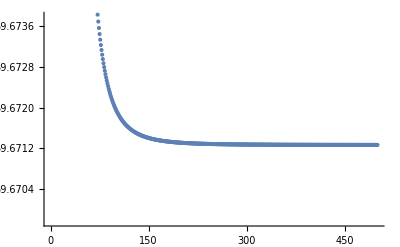

```mathematica
ListPlot[Nlist]
```